## MPO Tensors

### Square Lattice (FPL)

#### Vertex Tensor (FPL)

Starting from the vertex tensor for FPL (for β=0 only)

X[σ_i]=δ(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1) ⅇ^(ⅈ θ (σ_1+σ_2+σ_3+σ_4)/8),

with the angle θ parameterize the θ-term. σ_i=±1, and the labeling convesion as follows.

```mathematica
Null
```

-Graphics-

δ term make sure the edges are two-occupied-two-empty by the domain wall (σ_i σ_(i+1)=±1 for domain wall empty/occupation, so they must add to to 0). On the exponent, if ∑σ=0, spins are balanced, domain wall is straight, otherwise more up → positive angle, more down → negative angle.

Tensor code: Q=ⅈ θ

```mathematica
Module[{X},
X=Table[KroneckerDelta[σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1]EXP[Q((σ1+σ2+σ3+σ4)/8)],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"EXP(0)"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[1,2,3,4,6,7,8,9,11,12,13,14],[EXP(Q/4.),EXP(Q/4.),Z1,EXP(Q/4.),Z1,EXP(-Q/4.),EXP(Q/4.),Z1,EXP(-Q/4.),Z1,EXP(-Q/4.),EXP(-Q/4.)])

#### Make MPO

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Initialization

```mathematica
Null
```

Null

#### System Tensor

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

### Square Lattice (Loop Gas)

#### Vertex Tensor (LG)

Starting from the vertex tensor for O(n) model (loop gas)

X[σ_i]=ⅇ^(ⅈ θ (σ_1+σ_3-σ_1 σ_3(σ_2+σ_4))/8)ⅇ^(β(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1)/2),

with the angle θ parameterize the θ-term, and β is the string tension. σ_i=±1, and the labeling convesion as follows.

```mathematica
Null
```

-Graphics-

The strings are not intersecting. The ansatz is 𝒯-rev symmetric but breaks the C_4 rotational symmetry.

```mathematica
Module[{X},
X=Table[EXP[Q((σ1+σ3-σ1 σ3(σ2+σ4))/8)+B((σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1)/2)],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"0"->"Z0","1"->"Z1"}],"Program"]]
```

Null

#### Make MPO

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Test MPO

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### System Tensor

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Measurement

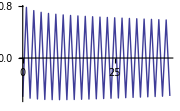
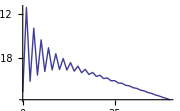
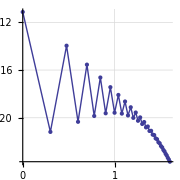

```mathematica
Module[{M0,M1,M2,val,vec,data},
{M0,M1,M2}=TensorLoad/@{"M0","M1","M2"};
{val,vec}=First@Thread@Eigensystem@M0;
M0=M0/val;
M1=M1/val;
M2=M2/val;
data=Table[{x,Chop[Conjugate[vec].M1.MatrixPower[M0,x].M2.vec]},{x,0,40}];
Print@{ListLinePlot[data,PlotRange->All,ImageSize->180],ListLinePlot[{#1,Log[10,Abs[#2]]}&@@@data,PlotRange->All,ImageSize->180],
ListLinePlot[{Log[10,#1],Log[10,Abs[#2]]}&@@@data,GridLines->{Range[0,5,0.1],Range[-10,0,0.1]},PlotRange->All,Mesh->Full,AspectRatio->Automatic,ImageSize->180]}
]
```

#### Solver

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

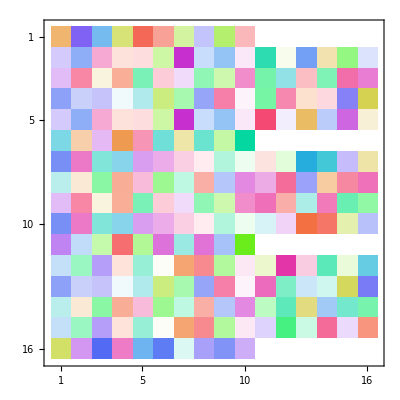
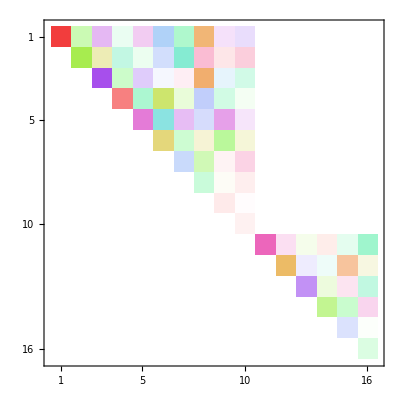

```mathematica
Null
```

### Square Lattice (Loop Gas, Avoid Crossing)

#### Vertex Tensor (LG)

Starting from the vertex tensor for O(n) model (loop gas)

X[σ_i]=ⅇ^(ⅈ θ (σ_1+σ_3-σ_1 σ_3(σ_2+σ_4))/8)ⅇ^(β(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1)/2)1/8((7+K)+(1-K)(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1-σ_1 σ_3-σ_2 σ_4-σ_1 σ_2 σ_3 σ_4)),

with the angle θ parameterize the θ-term, and β is the string tension. σ_i=±1, and the labeling convesion as follows.

```mathematica
Null
```

-Graphics-

The strings are not intersecting. The ansatz is 𝒯-rev symmetric but breaks the C_4 rotational symmetry.

```mathematica
Module[{X},
X=Table[EXP[Q((σ1+σ3-σ1 σ3(σ2+σ4))/8)+B((σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1)/2)]If[MatchQ[{{σ1,σ2},{σ4,σ3}},{{a_,b_},{b_,a_}}/;a==-b],CROSS,1],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"0"->"Z0","1"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15],[EXP(2*B),EXP(Q/4.),EXP(Q/4.),EXP(Z0),EXP(Q/4.),CROSS*EXP(-2*B - Q/2.),EXP(Z0),EXP(-Q/4.),EXP(Q/4.),EXP(Z0),CROSS*EXP(-2*B + Q/2.),EXP(-Q/4.),EXP(Z0),EXP(-Q/4.),EXP(-Q/4.),EXP(2*B)])

```mathematica
Module[{X},
X=Table[EXP[Q((σ1+σ3-σ1 σ3(σ2+σ4))/8)+B((σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1)/2)],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"0"->"Z0","1"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15],[EXP(2*B),EXP(Q/4.),EXP(Q/4.),EXP(Z0),EXP(Q/4.),EXP(-2*B - Q/2.),EXP(Z0),EXP(-Q/4.),EXP(Q/4.),EXP(Z0),EXP(-2*B + Q/2.),EXP(-Q/4.),EXP(Z0),EXP(-Q/4.),EXP(-Q/4.),EXP(2*B)])

```mathematica
Module[{ops,F,W},
ops=σ@@@Tuples[{0,3},4];
F=Normal[Diagonal/@Represent/@ops];
W=Flatten@Table[If[MatchQ[{{σ1,σ2},{σ4,σ3}},{{a_,b_},{b_,a_}}/;a==-b],K,1],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
Simplify[ops.F.W]]
```

2 ((7+K) σ[0,0,0,0]-(-1+K) (σ[0,0,3,3]-σ[0,3,0,3]+σ[0,3,3,0]+σ[3,0,0,3]-σ[3,0,3,0]+σ[3,3,0,0]-σ[3,3,3,3]))

## Test

#### Correlation

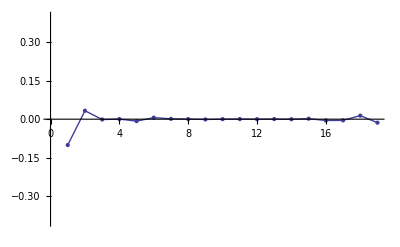

```mathematica
ListLinePlot[Most@Chop@FortranGet["C"],Mesh->All,PlotRange->{-0.4,0.4}]
```

{A→0.343054,α→1.1852,k→1.51059,ϕ→-1.47855}

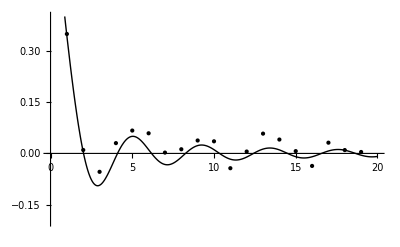

```mathematica
Module[{data,model,fit},
data=MapIndexed[{First[#2],#1}&,Rest@Reverse@Chop@FortranGet["C"]];
model=A x^(-α)Cos[k x+ϕ];
fit=FindFit[data,model,{{A,0.3},{α,2},{k,2π/4},{ϕ,0}},x];
Print[fit];
Plot[model/.fit,{x,0,20},PlotStyle->Black,PlotRange->{-0.2,0.4},Epilog->{PointSize[Absolute[4]],Map[Point,data]}]]
```

{A→-0.100722,α→57.0157,k→0.,ϕ→0.}

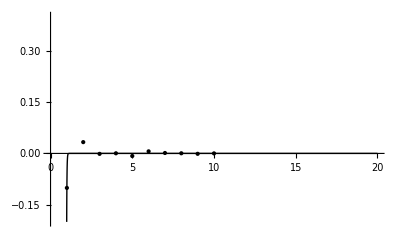

```mathematica
Module[{data,model,fit},
data=MapIndexed[{First[#2],#1}&,Chop@FortranGet["C"]⟦1;;10⟧];
model=A x^(-α)Cos[k x+ϕ];
fit=FindFit[data,model,{{A,0.2},{α,2},{k,0.},{ϕ,0}},x];
Print[fit];
Plot[model/.fit,{x,0,20},PlotStyle->Black,PlotRange->{-0.2,0.4},Epilog->{PointSize[Absolute[4]],Map[Point,data]}]]
```

```mathematica
FortranGet["A"]//Eigenvalues
```

{473.472+5.80036×10^-17 ⅈ,461.443+5.05447×10^-18 ⅈ,168.582-1.2517×10^-17 ⅈ,149.115+1.02341×10^-16 ⅈ,126.621+5.23689×10^-17 ⅈ,82.9563-4.82582×10^-17 ⅈ,78.8287-1.49735×10^-17 ⅈ,77.1139+6.05203×10^-18 ⅈ,75.5772-6.18525×10^-17 ⅈ,74.6498+5.50039×10^-18 ⅈ,74.6498+2.1774×10^-18 ⅈ,56.4392-8.898×10^-17 ⅈ,50.6951+7.86818×10^-17 ⅈ,48.8309+1.95512×10^-16 ⅈ,48.4053+3.28859×10^-17 ⅈ,42.9599+9.68346×10^-18 ⅈ,42.6253+6.27422×10^-17 ⅈ,39.7884+5.89806×10^-17 ⅈ,39.7884+1.65043×10^-16 ⅈ,37.6981+3.46733×10^-17 ⅈ,36.7539-4.75205×10^-18 ⅈ,33.2786+2.3505×10^-17 ⅈ,30.4114-3.78382×10^-16 ⅈ,25.718+7.16328×10^-17 ⅈ,22.7331+3.62033×10^-17 ⅈ,22.1207-4.81658×10^-17 ⅈ,20.6342-3.78929×10^-17 ⅈ,20.6342-3.67761×10^-16 ⅈ,19.9083+8.80045×10^-17 ⅈ,16.2659-1.25554×10^-17 ⅈ,13.5319+1.26265×10^-17 ⅈ,13.4963+7.91117×10^-17 ⅈ,12.8176+2.65208×10^-17 ⅈ,12.8128-7.08698×10^-18 ⅈ,9.96449+6.5301×10^-16 ⅈ,8.29019+8.14008×10^-17 ⅈ,7.85497-3.94763×10^-18 ⅈ,7.52342+2.58054×10^-17 ⅈ,7.12973+2.19194×10^-16 ⅈ,7.12973+4.98438×10^-17 ⅈ,6.30224+6.37197×10^-20 ⅈ,5.21328+3.59489×10^-17 ⅈ,4.52053-3.80891×10^-17 ⅈ,4.36664+1.37153×10^-17 ⅈ,4.29945-5.58143×10^-17 ⅈ,4.07357-1.79571×10^-17 ⅈ,3.87677+1.67176×10^-17 ⅈ,3.77284+1.08362×10^-16 ⅈ,3.63429+2.21734×10^-17 ⅈ,3.34841+1.11022×10^-15 ⅈ,3.34841-1.21778×10^-15 ⅈ,2.87178+6.44157×10^-18 ⅈ,2.55292+7.54126×10^-17 ⅈ,2.53081+8.3299×10^-18 ⅈ,2.17122-1.09077×10^-17 ⅈ,2.06255-2.35197×10^-17 ⅈ,1.95381+2.13718×10^-15 ⅈ,1.95381-1.9984×10^-15 ⅈ,1.84829+2.51249×10^-16 ⅈ,1.65396+6.18115×10^-18 ⅈ,1.08695+2.16595×10^-17 ⅈ,1.07732-4.35057×10^-18 ⅈ,0.353286+8.83976×10^-17 ⅈ,0.351607+2.24472×10^-17 ⅈ}

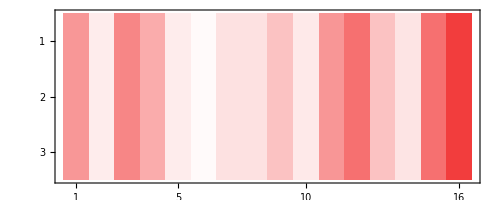

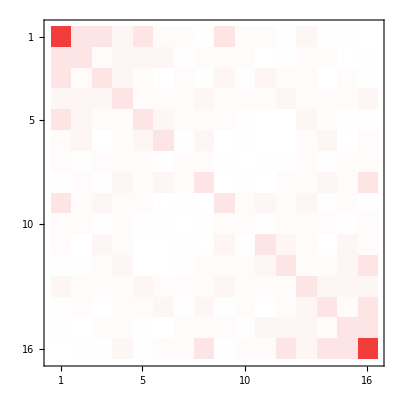
{-Graphics-,-Graphics-}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Module[{A,W0,WA,WB,l,r,Ts},
{A,W0,WA,WB,l,r,Ts}=FortranGet/@{"A","W0","WA","WB","LINDS","RINDS","TS"};
Print@ComplexMatrixPlot@{A.W0,WA,WB};
Print[ComplexMatrixPlot/@{A,SparseArray[{#1+1,#2+1}->#3&@@@Thread@{l,r,Ts}]}];
A-SparseArray[{#1+1,#2+1}->#3&@@@Thread@{l,r,Ts}]
]
```

#### Correlation

```mathematica
TensorLoad["M"]//Chop//MatrixForm
```

(0 | 0.121202 | 0.00502907 | 0.0088192 | 0.0257783 | 0.00656894 | -0.016798 | 0.000445434 | 0.0203086 | 0.0176966 | 0.0330456 | 0.270312
0 | 0 | 0.135705 | 0.0226368 | 0.01319 | 0.0178268 | -0.00924208 | -0.0150227 | -0.00521249 | 0.0106668 | 0.0153732 | 0.0258192
0 | 0 | 0 | 0.130308 | 0.01319 | 0.0144296 | 0.00849466 | -0.0059212 | -0.0123088 | -0.00337262 | 0.00657132 | 0.00232762
0 | 0 | 0 | 0 | 0.140788 | 0.0313699 | 0.0138319 | 0.0106848 | -0.00326121 | -0.011148 | -0.000813543 | 0.0385378
0 | 0 | 0 | 0 | 0 | 0.132176 | 0.0201834 | 0.0158866 | 0.0105897 | -0.00282986 | -0.00675698 | 0.0276946
0 | 0 | 0 | 0 | 0 | 0 | 0.126715 | 0.016129 | 0.00764518 | 0.0100954 | -0.000277466 | -0.003983
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.137119 | 0.0179886 | 0.00904855 | 0.0019584 | -0.0118147
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.136656 | 0.0187372 | -0.00411729 | 0.0165848
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.138524 | 0.0208943 | 0.0158102
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.142669 | 0.0586944
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.304238
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ListPlot3D[TensorLoad["M"]//Chop,PlotRange->All]
```

-Graphics3D-

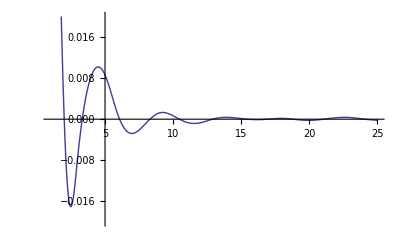

```mathematica
Module[{M,L},
M=TensorLoad["M"];
L=Length[M];
ListLinePlot[Chop@Mean[Join[Diagonal[M,#],Diagonal[M,L-#]]]&/@Range[L/2],PlotRange->{-0.02,0.02},InterpolationOrder->3]]
```

{25,0.359274}

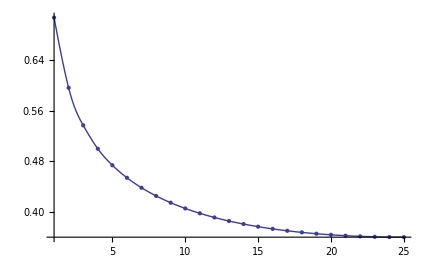

-0.346907-0.248186 x

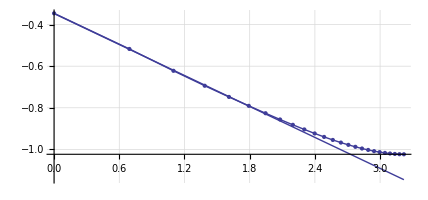

```mathematica
Module[{M,L,data,ldata,fit},
M=TensorLoad["M"];
L=Length[M];
data=MapIndexed[{First[#2],#1}&,Re@Mean[Join[Diagonal[M,#],Diagonal[M,L-#]]]&/@Range[L/2]];
Print[Last[data]];
Print@ListLinePlot[data,PlotRange->All,InterpolationOrder->3,Mesh->Full];
ldata={Log[#1],Log[#2]}&@@@data;
Print[fit=Fit[ldata⟦;;7⟧,{1,x},x]];
Show[ListLinePlot[ldata,GridLines->{Range[0,4,0.1],Range[-20,7,0.1]},AspectRatio->Automatic,PlotRange->All,InterpolationOrder->1,Mesh->Full],Plot[fit,{x,ldata⟦1,1⟧,ldata⟦-1,1⟧}]]]
```

#### Correlation

```mathematica
TensorLoad["M"]//Chop//MatrixForm
```

(0 | 0.0786962 | 0.0220867 | 0.0412694 | 0.0331254 | -0.00106029 | 0.00257107 | 0.0201361 | 0.00688991 | -0.0101635 | 0.00283909 | 0.0146825 | -0.000890093 | -0.0111671 | 0.00442632 | 0.0125349 | -0.00396 | -0.0111075 | 0.00576788 | 0.0120021 | -0.00539824 | -0.010828 | 0.00675016 | 0.0111894 | -0.00670108-3.71736×10^-10 ⅈ | -0.00960446 | 0.00797119 | 0.00959538 | -0.00790912 | -0.0079081 | 0.00918628 | 0.00804522 | -0.00891144 | -0.00679625 | 0.00999248 | 0.00714481 | -0.00945929 | -0.00649012 | 0.0103481 | 0.00755771 | -0.00927168 | -0.0074092 | 0.00979121 | 0.00959899 | -0.00773736 | -0.00977844 | 0.00742755 | 0.0121837 | -0.00436597 | -0.012587 | 0.0022879 | 0.0134882 | -0.000112941 | -0.0162999 | -0.00904123 | 0.00703883 | -0.00112761 | -0.0342228 | -0.0613161 | 0.140562
0 | 0 | 0.0909423 | 0.0275966 | 0.0339541 | 0.034184 | 0.0106936 | -0.00143988 | 0.00950954 | 0.0132284 | -0.00023044 | -0.00600481 | 0.00458629 | 0.00846628 | -0.00290827 | -0.00710869 | 0.00373147 | 0.00746553 | -0.00390289 | -0.00757421 | 0.00388983 | 0.00716781 | -0.00451334 | -0.00729777 | 0.00452781+5.75367×10^-10 ⅈ | 0.00635075 | -0.00529443 | -0.00631803 | 0.00526787 | 0.00523384 | -0.00609093 | -0.00531643 | 0.00591551 | 0.00450185 | -0.00662352 | -0.0047295 | 0.00627349 | 0.004301 | -0.00685931 | -0.00500727 | 0.00614719 | 0.00491093 | -0.0064904 | -0.00636209 | 0.00512933 | 0.00648171 | -0.00492362 | -0.00807605 | 0.00289423 | 0.0083435 | -0.00151665 | -0.00894093 | 0.0000748984 | 0.0108048 | 0.00599317 | -0.00466585 | 0.000747467 | 0.0226853 | 0.0406448 | -0.0931746
0 | 0 | 0 | 0.089136 | 0.0277619 | 0.0318462 | 0.0296966 | 0.00811376 | 0.00247094 | 0.0102155 | 0.00693525 | -0.00102253 | 0.00094258 | 0.00502137 | 0.000884089 | -0.00268838 | 0.00104323 | 0.00343679 | -0.000910701 | -0.00298805 | 0.00130588 | 0.00292559 | -0.00155196 | -0.00284026 | 0.00167783+2.93163×10^-10 ⅈ | 0.00249801 | -0.0019704 | -0.00243492 | 0.00199858 | 0.00202678 | -0.00230919 | -0.00203877 | 0.00225406 | 0.00172906 | -0.00252233 | -0.00180872 | 0.00239262 | 0.00164527 | -0.00261534 | -0.00191207 | 0.00234497 | 0.00187526 | -0.00247567 | -0.00242798 | 0.00195682 | 0.00247355 | -0.00187834 | -0.00308159 | 0.00110418 | 0.0031836 | -0.000578575 | -0.00341146 | 0.0000285362 | 0.00412262 | 0.00228676 | -0.00178026 | 0.000285187 | 0.00865569 | 0.0155082 | -0.0355512
0 | 0 | 0 | 0 | 0.0921202 | 0.0288079 | 0.0329482 | 0.0334892 | 0.0121528 | 0.000187359 | 0.00966935 | 0.0135904 | 0.00089996 | -0.00490859 | 0.00499777 | 0.00877582 | -0.00224087 | -0.00626568 | 0.00423637 | 0.00763796 | -0.00337068 | -0.00652041 | 0.00438499 | 0.00697222 | -0.00416865 | -0.00588509 | 0.00500908 | 0.0059596 | -0.00490995 | -0.00487898 | 0.00572367 | 0.00499478 | -0.00553238 | -0.00420793 | 0.00621213 | 0.00443619 | -0.0058734 | -0.00402558 | 0.00642876 | 0.0046931 | -0.00575748 | -0.00459942 | 0.00608128 | 0.00596084 | -0.00480494 | -0.0060719 | 0.00461278 | 0.00756601 | -0.00271132 | -0.00781632 | 0.00142088 | 0.0083761 | -0.0000701684 | -0.0101221 | -0.00561452 | 0.00437109 | -0.000700258 | -0.0212522 | -0.0380769 | 0.087288
0 | 0 | 0 | 0 | 0 | 0.0884721 | 0.0270383 | 0.0294263 | 0.0297553 | 0.00984254 | 0.00156987 | 0.00826196 | 0.00741893 | 0.0000340923 | -0.0000587293 | 0.00367077 | 0.00163509 | -0.00138331 | 0.000356833 | 0.00219301 | -0.0000430102 | -0.00142029 | 0.000701472 | 0.00161644 | -0.000652888 | -0.00123942 | 0.000948053 | 0.00127116 | -0.000925842 | -0.00100113 | 0.00112644 | 0.00102748 | -0.00108355 | -0.000848638 | 0.0012326 | 0.000895858 | -0.00116155 | -0.000804725 | 0.00127737 | 0.000938359 | -0.00114221 | -0.000916037 | 0.00120851 | 0.00118686 | -0.000954349 | -0.00120771 | 0.000916764 | 0.00150472 | -0.000538731 | -0.00155418 | 0.000282324 | 0.00166539 | -0.0000138683 | -0.00201251 | -0.00111633 | 0.000869048 | -0.000139215 | -0.00422533 | -0.0075704 | 0.0173545
0 | 0 | 0 | 0 | 0 | 0 | 0.0892505 | 0.026243 | 0.0285629 | 0.0311193 | 0.00981592 | -0.00096991 | 0.0079418 | 0.010906 | -0.000676694 | -0.00488347 | 0.00414523 | 0.00693218 | -0.00294392 | -0.00599038 | 0.00345716 | 0.00606129 | -0.00367995 | -0.00594253 | 0.00380735 | 0.00527118 | -0.00435528 | -0.00518072 | 0.00436886 | 0.00432468 | -0.00501857 | -0.00437207 | 0.00488688 | 0.003715 | -0.00546002 | -0.00389521 | 0.00517675 | 0.00354772 | -0.00565575 | -0.00412735 | 0.0050706 | 0.00405013 | -0.00535221 | -0.00524598 | 0.00423039 | 0.00534532 | -0.00406037 | -0.00665993 | 0.0023869 | 0.00688065 | -0.00125076 | -0.00737331 | 0.0000617862 | 0.00891038 | 0.0049424 | -0.0038478 | 0.000616412 | 0.018708 | 0.0335186 | -0.0768386
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0923593 | 0.0301908 | 0.0296116 | 0.0302606 | 0.0122478 | 0.0025696 | 0.00720112 | 0.0077056 | 0.00202337 | 0.0000371729 | 0.00238608 | 0.00211471 | 0.0000133777 | -0.00019121 | 0.00090995 | 0.000508497 | -0.000268801 | 0.0000416792 | 0.000466781 | 0.0000282979 | -0.000236524 | 0.000146064 | 0.000271397 | -0.000130022 | -0.000186394 | 0.000181497 | 0.000182342 | -0.000186051 | -0.000156475 | 0.000195017 | 0.000149943 | -0.000206237 | -0.000159493 | 0.000191176 | 0.000158762 | -0.000199521 | -0.000199679 | 0.000159387 | 0.000203881 | -0.000152627 | -0.000252389 | 0.0000899781 | 0.000260809 | -0.0000469632 | -0.00027911 | 2.20369×10^-6 | 0.000337338 | 0.000187218 | -0.000145602 | 0.0000232826 | 0.000708125 | 0.00126877 | -0.00290847
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0918364 | 0.0276757 | 0.0287758 | 0.0305626 | 0.0116933 | -0.000722688 | 0.0072754 | 0.0116111 | 0.000461207 | -0.00467831 | 0.00424879 | 0.00751013 | -0.00231947 | -0.00535963 | 0.00387866 | 0.00615491 | -0.00339529 | -0.00492289 | 0.0042894 | 0.00511249 | -0.00411097 | -0.00410309 | 0.00485806 | 0.00424664 | -0.00466203 | -0.00354776 | 0.00525854 | 0.00375853 | -0.0049585 | -0.00339868 | 0.00543646 | 0.00396983 | -0.0048639 | -0.00388596 | 0.00514053 | 0.00503882 | -0.00406029 | -0.00513128 | 0.00389863 | 0.00639458 | -0.0022913 | -0.0066058 | 0.00120086 | 0.00707898 | -0.0000592934 | -0.00855457 | -0.004745 | 0.00369417 | -0.000591828 | -0.0179609 | -0.0321801 | 0.0737701
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0900651 | 0.0282322 | 0.0281166 | 0.029255 | 0.0114429 | 0.000859644 | 0.00618459 | 0.00759685 | 0.00161938 | -0.00100021 | 0.00164983 | 0.00227891 | 0.000302883 | -0.000685756 | 0.000274479 | 0.000815273 | 0.000198914 | -0.00042554 | -0.0000903921 | 0.000453126 | 0.000207088 | -0.000367874 | -0.000188199 | 0.000377325 | 0.000213398 | -0.000371015 | -0.000217729 | 0.000363522 | 0.000223171 | -0.000378836 | -0.000258814 | 0.000344832 | 0.00026463 | -0.00035783 | -0.000343823 | 0.000284312 | 0.000354031 | -0.000271171 | -0.000441662 | 0.00015977 | 0.000457242 | -0.0000837363 | -0.000490276 | 4.36198×10^-6 | 0.000592588 | 0.000328595 | -0.000255975 | 0.0000410358 | 0.00124444 | 0.00222966 | -0.00511139
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0914426 | 0.0286273 | 0.0285265 | 0.0302956 | 0.0106943 | 0.0000547491 | 0.00739788 | 0.0103457 | -0.000324543 | -0.0044763 | 0.0037917 | 0.00633576 | -0.00282172 | -0.00514351 | 0.00358907 | 0.00497046 | -0.00378348 | -0.00458929 | 0.00397805 | 0.00395423 | -0.0044619 | -0.00389976 | 0.00440272 | 0.0033563 | -0.00488177 | -0.00348474 | 0.00464895 | 0.00318963 | -0.00506589 | -0.00369763 | 0.0045488 | 0.00363419 | -0.00479724 | -0.00470276 | 0.0037936 | 0.00479347 | -0.00364024 | -0.00597126 | 0.00214024 | 0.00616953 | -0.00112138 | -0.00661109 | 0.000055388 | 0.00798933 | 0.00443155 | -0.00345003 | 0.000552669 | 0.0167742 | 0.0300539 | -0.0688959
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0915402 | 0.0298021 | 0.0274532 | 0.0288383 | 0.0130365 | 0.00222414 | 0.00546668 | 0.00790129 | 0.00330022 | -0.000785973 | 0.000908383 | 0.00274532 | 0.00133005 | -0.000876941 | -0.000237397 | 0.00140985 | 0.00093539 | -0.000865889 | -0.000522142 | 0.00113058 | 0.000785846 | -0.000936959 | -0.000591427 | 0.00109757 | 0.000717859 | -0.000987366 | -0.000631885 | 0.00109758 | 0.000776018 | -0.000966853 | -0.000755485 | 0.00102641 | 0.000994585 | -0.000806838 | -0.00101248 | 0.000775208 | 0.00126583 | -0.000455073 | -0.00130771 | 0.000238951 | 0.00140235 | -0.0000121382 | -0.00169458 | -0.000939664 | 0.000731972 | -0.000117378 | -0.00355829 | -0.00637518 | 0.0146148
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0930136 | 0.0276163 | 0.026721 | 0.0298073 | 0.0120197 | -0.000795899 | 0.00652135 | 0.0112148 | 0.000453937 | -0.00453659 | 0.00399413 | 0.00680043 | -0.00259642 | -0.00457974 | 0.00410107 | 0.00509763 | -0.0037124 | -0.00386211 | 0.00459433 | 0.00409182 | -0.00433907 | -0.0033416 | 0.00495757 | 0.00357097 | -0.00464895 | -0.00319956 | 0.00511849 | 0.00374756 | -0.00457055 | -0.00365731 | 0.00483717 | 0.00474489 | -0.00381842 | -0.00482853 | 0.00366799 | 0.00601769 | -0.00215533 | -0.00621566 | 0.00112968 | 0.00666084 | -0.0000556691 | -0.00804916 | -0.00446468 | 0.0034759 | -0.000556861 | -0.0168996 | -0.0302786 | 0.069411
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0920888 | 0.0284963 | 0.0273939 | 0.0294168 | 0.0126376 | 0.000338354 | 0.00492476 | 0.00782349 | 0.00247822 | -0.00164817 | 0.00066942 | 0.00272511 | 0.000949304 | -0.00132495 | -0.000381501 | 0.00148009 | 0.000734768 | -0.00119401 | -0.00064317 | 0.00122151 | 0.000704162 | -0.00120745 | -0.000719224 | 0.00117514 | 0.000725147 | -0.00123104 | -0.000844648 | 0.00111593 | 0.000858003 | -0.00116119 | -0.00111672 | 0.000921053 | 0.00114788 | -0.000879449 | -0.00143261 | 0.000517816 | 0.00148262 | -0.000271516 | -0.00158982 | 0.0000141112 | 0.00192149 | 0.00106546 | -0.000830024 | 0.000133075 | 0.00403509 | 0.00722964 | -0.0165736
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0920648 | 0.0280746 | 0.0277085 | 0.0301662 | 0.0109478 | -0.0000976326 | 0.0067157 | 0.00982773 | -0.000345384 | -0.00392936 | 0.00400508 | 0.00551889 | -0.00298377 | -0.00402334 | 0.00382312 | 0.00387418 | -0.00394873 | -0.0035141 | 0.0040688 | 0.00313916 | -0.00441243 | -0.00316515 | 0.00425299 | 0.0029319 | -0.00460496 | -0.0033671 | 0.00414968 | 0.00331958 | -0.00436855 | -0.00428572 | 0.00345795 | 0.0043707 | -0.00331686 | -0.00544241 | 0.00195059 | 0.00562351 | -0.0010218 | -0.00602561 | 0.0000503948 | 0.00728187 | 0.00403922 | -0.00314447 | 0.00050367 | 0.0152887 | 0.0273925 | -0.0627948
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0928516 | 0.0304837 | 0.0278788 | 0.0293591 | 0.0140681 | 0.00202763 | 0.00478445 | 0.00817696 | 0.00400694 | -0.000956129 | 0.000566542 | 0.00329594 | 0.00188359 | -0.00141814 | -0.000584979 | 0.00217816 | 0.00137419 | -0.00161723 | -0.000914162 | 0.00196475 | 0.00122861 | -0.00171313 | -0.00105527 | 0.00192095 | 0.00133411 | -0.00167799 | -0.00129507 | 0.00178425 | 0.00171774 | -0.00139977 | -0.00174923 | 0.00134457 | 0.00219007 | -0.00078914 | -0.00226298 | 0.000414651 | 0.0024275 | -0.0000214453 | -0.00293337 | -0.00162633 | 0.00126723 | -0.000203316 | -0.00615987 | -0.0110362 | 0.0253002
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0938338 | 0.0279844 | 0.0262485 | 0.0297825 | 0.011977 | -0.000709232 | 0.00638237 | 0.0104939 | -0.0000148112 | -0.00384081 | 0.00427104 | 0.00584796 | -0.00294016 | -0.00362215 | 0.00441592 | 0.00417168 | -0.00394336 | -0.00316954 | 0.00470116 | 0.00347205 | -0.00433788 | -0.00302864 | 0.00483389 | 0.00356947 | -0.00429544 | -0.00345528 | 0.004562 | 0.00448582 | -0.00359667 | -0.00455674 | 0.00345847 | 0.00567868 | -0.00203149 | -0.00586371 | 0.00106478 | 0.00628323 | -0.0000521602 | -0.00759265 | -0.00421158 | 0.00327865 | -0.000525243 | -0.0159407 | -0.0285604 | 0.0654722
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0929236 | 0.0282211 | 0.0273736 | 0.0294593 | 0.0130408 | 0.000430334 | 0.0046739 | 0.00801933 | 0.00290316 | -0.00180412 | 0.000537998 | 0.00323077 | 0.00119169 | -0.00185837 | -0.000578775 | 0.00210494 | 0.000998536 | -0.00184722 | -0.000938263 | 0.00184811 | 0.00105093 | -0.00186783 | -0.00121986 | 0.00170523 | 0.00127204 | -0.00175692 | -0.00166424 | 0.00139513 | 0.00172018 | -0.00132812 | -0.00215121 | 0.00078228 | 0.0022284 | -0.000410736 | -0.00239112 | 0.0000221624 | 0.00289003 | 0.00160197 | -0.00124878 | 0.000200373 | 0.00606993 | 0.0108754 | -0.0249318
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0931034 | 0.0281475 | 0.0272987 | 0.0296365 | 0.0104785 | -0.0000639244 | 0.00707091 | 0.00952902 | -0.00075611 | -0.00329006 | 0.00442621 | 0.00483381 | -0.00336611 | -0.00332675 | 0.00411092 | 0.00334581 | -0.00415883 | -0.00307433 | 0.00416393 | 0.00293615 | -0.00443432 | -0.00327796 | 0.00403366 | 0.0032499 | -0.00423125 | -0.00416748 | 0.00335621 | 0.00425169 | -0.00321827 | -0.00528824 | 0.00189311 | 0.0054638 | -0.000991278 | -0.00585331 | 0.000048401 | 0.00707359 | 0.00392401 | -0.00305432 | 0.000489072 | 0.0148509 | 0.0266081 | -0.0609964
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0927166 | 0.0304233 | 0.0277016 | 0.0287983 | 0.0138181 | 0.00201285 | 0.0049765 | 0.00824441 | 0.00400427 | -0.00122739 | 0.000646703 | 0.00382601 | 0.00195938 | -0.00198076 | -0.000707215 | 0.00279268 | 0.00154416 | -0.00218951 | -0.00119084 | 0.00253688 | 0.00167023 | -0.00215505 | -0.00160106 | 0.00230454 | 0.00217483 | -0.00179669 | -0.00221652 | 0.00172435 | 0.00278705 | -0.00101157 | -0.0028818 | 0.000532545 | 0.0030941 | -0.0000291125 | -0.00373899 | -0.00207194 | 0.0016159 | -0.00025967 | -0.00785301 | -0.0140695 | 0.0322547
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0931916 | 0.0276788 | 0.0262598 | 0.0293955 | 0.0112249 | -0.000209363 | 0.0071078 | 0.010175 | -0.000415569 | -0.00313686 | 0.00489031 | 0.00536898 | -0.00330244 | -0.00316146 | 0.00476858 | 0.0038214 | -0.00413658 | -0.00304612 | 0.00481399 | 0.00365931 | -0.00421323 | -0.00345351 | 0.00452302 | 0.00448563 | -0.00355497 | -0.00453322 | 0.00342745 | 0.00564504 | -0.0020121 | -0.00582445 | 0.00105401 | 0.00623886 | -0.0000506364 | -0.00753876 | -0.00418223 | 0.00325487 | -0.000521308 | -0.015826 | -0.0283547 | 0.0650002
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0928147 | 0.0281592 | 0.0282328 | 0.0297625 | 0.0131913 | 0.000916134 | 0.00536706 | 0.00856165 | 0.00300065 | -0.00194153 | 0.000829766 | 0.00378298 | 0.00128999 | -0.00228803 | -0.000631334 | 0.00259196 | 0.00120638 | -0.0023359 | -0.00132688 | 0.0021897 | 0.00150838 | -0.00219062 | -0.00199363 | 0.00174518 | 0.00209161 | -0.00164876 | -0.00263011 | 0.00097143 | 0.00273039 | -0.000512301 | -0.00293537 | 0.0000302607 | 0.0035477 | 0.00196463 | -0.00153434 | 0.000246736 | 0.00745428 | 0.0133554 | -0.030619
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0929692 | 0.0288693 | 0.0289549 | 0.0303142 | 0.010306 | 0.000751752 | 0.00806569 | 0.00945344 | -0.000950886 | -0.00255892 | 0.00483393 | 0.00450831 | -0.00349761 | -0.00293246 | 0.00421398 | 0.00320414 | -0.00417682 | -0.00322146 | 0.00394395 | 0.00326177 | -0.00408487 | -0.004085 | 0.00326162 | 0.00416865 | -0.00312732 | -0.00516662 | 0.00183981 | 0.00533449 | -0.000962657 | -0.00571143 | 0.0000449944 | 0.00690137 | 0.00382948 | -0.00297935 | 0.000476535 | 0.0144874 | 0.0259569 | -0.0595029
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0916894 | 0.0302096 | 0.0287438 | 0.0289311 | 0.0136187 | 0.00224316 | 0.00572906 | 0.00881515 | 0.00406433 | -0.00150269 | 0.000782178 | 0.00441376 | 0.00205997 | -0.00240817 | -0.000872844 | 0.00326567 | 0.00192585 | -0.00251375 | -0.00170393 | 0.00276702 | 0.00249064 | -0.00211295 | -0.0025294 | 0.00202743 | 0.00321548 | -0.00118788 | -0.00332935 | 0.000627974 | 0.00358188 | -0.0000391406 | -0.00432895 | -0.00239573 | 0.00187259 | -0.000302197 | -0.00909565 | -0.016295 | 0.0373593
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0914937 | 0.0275891 | 0.0276755 | 0.0295672 | 0.0109038 | 0.000666947 | 0.00786192 | 0.010002 | -0.000426135 | -0.00259132 | 0.00507931 | 0.00503165 | -0.00321542 | -0.00294397 | 0.00461106 | 0.00386043 | -0.00379019 | -0.00333392 | 0.00424171 | 0.00433713 | -0.00330057 | -0.00430896 | 0.00320943 | 0.00534642 | -0.00188244 | -0.00550394 | 0.000982736 | 0.0058862 | -0.0000439955 | -0.00711266 | -0.00394805 | 0.00306886 | -0.000490991 | -0.014926 | -0.0267421 | 0.0613014
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0922893 | 0.0286162 | 0.0292065 | 0.0303833 | 0.013461 | 0.00102033 | 0.0057926 | 0.00916045 | 0.00317723 | -0.00231274 | 0.000751697 | 0.00431181 | 0.00156224 | -0.00286391 | -0.00114854 | 0.00295737 | 0.00174743 | -0.0027356 | -0.00229491 | 0.00220397 | 0.00249194 | -0.0020475 | -0.00316481 | 0.00120623 | 0.00329774 | -0.000642935 | -0.00355999 | 0.0000446312 | 0.00430093 | 0.00237616 | -0.00186408 | 0.000301203 | 0.00904433 | 0.0162028 | -0.0371522
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0924879 | 0.029203 | 0.0296529 | 0.0306856 | 0.010571 | 0.00157316 | 0.00827366 | 0.00923513 | -0.000493216 | -0.00200648 | 0.00453956 | 0.0042388 | -0.00306333 | -0.00286455 | 0.00357933 | 0.0032489 | -0.00345963 | -0.00368581 | 0.00285574 | 0.00377841 | -0.00273258 | -0.00461584 | 0.00160827 | 0.00475248 | -0.000839428 | -0.00507705 | 0.0000317364 | 0.00613144 | 0.00340568 | -0.00264509 | 0.000421174 | 0.0128645 | 0.023049 | -0.0528347
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0913626 | 0.0297087 | 0.0292228 | 0.0293122 | 0.0137931 | 0.00196472 | 0.00553918 | 0.00940743 | 0.00428673 | -0.00205599 | 0.000370347 | 0.00494301 | 0.00256155 | -0.00289068 | -0.00162123 | 0.00354342 | 0.00292836 | -0.00254852 | -0.00289029 | 0.00246325 | 0.00376232 | -0.00143749 | -0.00390017 | 0.000765942 | 0.00421102 | -0.0000601671 | -0.00509055 | -0.00280908 | 0.00220587 | -0.000359354 | -0.0107025 | -0.0191714 | 0.0439604
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0916459 | 0.0278895 | 0.0275763 | 0.0296037 | 0.0112494 | 0.000785103 | 0.00729972 | 0.00944914 | -0.0000253666 | -0.00248066 | 0.00427319 | 0.0047394 | -0.00257605 | -0.00310749 | 0.00354803 | 0.00408836 | -0.00265559 | -0.00382588 | 0.00267334 | 0.00467309 | -0.00156573 | -0.0047738 | 0.000803676 | 0.00507135 | -0.0000237504 | -0.00612981 | -0.00341169 | 0.00263682 | -0.000419591 | -0.0128446 | -0.023014 | 0.0527467
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0925676 | 0.0286508 | 0.0290494 | 0.0305906 | 0.0136784 | 0.00064076 | 0.00516879 | 0.0093168 | 0.003421 | -0.00304323 | -0.000136332 | 0.00448851 | 0.00211874 | -0.00335925 | -0.00239817 | 0.00283602 | 0.0028527 | -0.00252536 | -0.0036645 | 0.00148878 | 0.00384231 | -0.000811794 | -0.00418197 | 0.0000736001 | 0.00504438 | 0.00277002 | -0.0021977 | 0.000358943 | 0.0106238 | 0.019026 | -0.0436424
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0929968 | 0.0294679 | 0.0290551 | 0.0301547 | 0.0112342 | 0.00169239 | 0.00722304 | 0.00866626 | 0.000159921 | -0.00203059 | 0.00340586 | 0.00396999 | -0.00219176 | -0.00315049 | 0.00225254 | 0.0033825 | -0.00209065 | -0.00388673 | 0.00124272 | 0.00396986 | -0.00063833 | -0.00420192 | -1.69489×10^-6 | 0.00506446 | 0.00282495 | -0.00217856 | 0.000340434 | 0.0106043 | 0.0189993 | -0.043544
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0918869 | 0.0292925 | 0.0280224 | 0.0290055 | 0.0139153 | 0.00122773 | 0.00436741 | 0.00951482 | 0.00476881 | -0.00275095 | -0.000856167 | 0.00500044 | 0.00364324 | -0.00299687 | -0.00312823 | 0.00305067 | 0.00432958 | -0.00174326 | -0.00445838 | 0.000948648 | 0.00484589 | -0.000104993 | -0.00585686 | -0.00320971 | 0.00254709 | -0.000423798 | -0.0123233 | -0.0220661 | 0.0506159
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0928801 | 0.0280893 | 0.0265673 | 0.0289282 | 0.0117251 | 0.00047699 | 0.00575147 | 0.00874712 | 0.000541029 | -0.0028802 | 0.00279169 | 0.0045908 | -0.00156815 | -0.00352962 | 0.00195754 | 0.00413975 | -0.00113574 | -0.00412027 | 0.000535708 | 0.00427283 | 0.0000285377 | -0.00517456 | -0.00291412 | 0.00219873 | -0.000341647 | -0.0107868 | -0.0193348 | 0.0442806
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0933421 | 0.0285412 | 0.0275798 | 0.0301442 | 0.0139484 | -0.000214744 | 0.00366819 | 0.00904469 | 0.00390306 | -0.00369039 | -0.00180187 | 0.00407945 | 0.00325009 | -0.00311623 | -0.00399749 | 0.00189133 | 0.00427433 | -0.00106823 | -0.00472026 | 0.000144084 | 0.00566559 | 0.00305768 | -0.00250093 | 0.000419496 | 0.0119621 | 0.0213992 | -0.0491415
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0933314 | 0.0292211 | 0.0273608 | 0.0290068 | 0.0116907 | 0.00126076 | 0.00551037 | 0.00802349 | 0.000835769 | -0.00249286 | 0.00191462 | 0.00385469 | -0.00118179 | -0.00348202 | 0.000851443 | 0.0035792 | -0.000371548 | -0.00365479 | -0.0000880112 | 0.00438893 | 0.00248927 | -0.00186586 | 0.000271615 | 0.00912732 | 0.0163577 | -0.037463
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0923079 | 0.0289352 | 0.0262349 | 0.0283044 | 0.0143339 | 0.000416119 | 0.00252544 | 0.00908904 | 0.0057626 | -0.00298985 | -0.00274526 | 0.00410862 | 0.00493393 | -0.00207189 | -0.0047755 | 0.00123653 | 0.00529549 | -0.000215437 | -0.00636848 | -0.00341804 | 0.00279881 | -0.000490831 | -0.0134101 | -0.0239766 | 0.0550572
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0940144 | 0.0281235 | 0.024567 | 0.027942 | 0.0123402 | -0.000130625 | 0.00373266 | 0.00817313 | 0.0013301 | -0.00343113 | 0.00113059 | 0.00441835 | -0.000370999 | -0.00393224 | 0.000059947 | 0.00383095 | 0.000180379 | -0.00466874 | -0.00274571 | 0.00190332 | -0.000266246 | -0.00959321 | -0.0172254 | 0.0393322
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0941197 | 0.0279715 | 0.0254841 | 0.0289549 | 0.0143172 | -0.00104263 | 0.00130627 | 0.00799098 | 0.00482632 | -0.00356389 | -0.00375063 | 0.00282279 | 0.00457435 | -0.00153149 | -0.00506284 | 0.000344169 | 0.00601033 | 0.00307125 | -0.00274272 | 0.000496503 | 0.0127173 | 0.0226675 | -0.0522365
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0935895 | 0.0288649 | 0.0250949 | 0.0277336 | 0.0122748 | 0.000611576 | 0.00333359 | 0.00729725 | 0.00145168 | -0.00306284 | 0.000521582 | 0.00399391 | 0.000265168 | -0.00351377 | -0.00031912 | 0.00427843 | 0.00256562 | -0.00174318 | 0.000197268 | 0.00873366 | 0.0156849 | -0.0358224
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0928621 | 0.0287726 | 0.024007 | 0.0271006 | 0.0153831 | 0.000189622 | 0.000100901 | 0.00773874 | 0.00696036 | -0.00205386 | -0.00461944 | 0.00203586 | 0.00576476 | -0.000455535 | -0.00663022 | -0.00331737 | 0.00301344 | -0.000596445 | -0.013934 | -0.0247769 | 0.0571018
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0945234 | 0.0278543 | 0.0216357 | 0.0266518 | 0.0130897 | -0.000772623 | 0.00172882 | 0.00769356 | 0.00228188 | -0.00428112 | -0.000819096 | 0.00425316 | 0.000723373 | -0.00507909 | -0.00333886 | 0.00185413 | -0.000160905 | -0.0101513 | -0.018357 | 0.0415548
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0945414 | 0.0275426 | 0.0223286 | 0.0267432 | 0.0150408 | -0.00123927 | -0.00117873 | 0.0064031 | 0.00577071 | -0.00213147 | -0.00496784 | 0.00107278 | 0.00600792 | 0.00253633 | -0.00298223 | 0.000644614 | 0.012583 | 0.022103 | -0.0515227
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0944505 | 0.028315 | 0.0222393 | 0.026339 | 0.0128373 | 8.41795×10^-6 | 0.00166852 | 0.00712455 | 0.00277884 | -0.00343072 | -0.000704158 | 0.00510263 | 0.00352492 | -0.00180997 | 0.0000334671 | 0.00998731 | 0.0180605 | -0.0409006
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0942032 | 0.0293334 | 0.0214618 | 0.025798 | 0.0166551 | 0.000930996 | -0.00220213 | 0.00548877 | 0.00755374 | -0.000586797 | -0.00644625 | -0.00229267 | 0.00343406 | -0.000853653 | -0.0134376 | -0.0233 | 0.0545358
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0959546 | 0.027534 | 0.0188954 | 0.025484 | 0.0136093 | -0.00233732 | -0.000647014 | 0.00732661 | 0.0030121 | -0.00655395 | -0.0049772 | 0.00213311 | 0.0000282317 | -0.0128775 | -0.0235846 | 0.0526158
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0951618 | 0.0273677 | 0.0199788 | 0.0250349 | 0.0151426 | -0.000419411 | -0.00262032 | 0.00445122 | 0.00609169 | 0.00113146 | -0.0032186 | 0.000970642 | 0.0109792 | 0.0182588 | -0.0444405
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0950649 | 0.0282606 | 0.0207398 | 0.0252033 | 0.0137778 | -0.000409423 | 0.000193266 | 0.00789676 | 0.00659073 | -0.0013583 | -0.000307523 | 0.0130333 | 0.0242981 | -0.0539949
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0958093 | 0.0301291 | 0.019021 | 0.0240272 | 0.0172757 | 0.00174087 | -0.00478607 | 0.00188248 | 0.00611419 | -0.00107512 | -0.0117884 | -0.017231 | 0.0441887
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0951541 | 0.0257104 | 0.0160079 | 0.023793 | 0.0134654 | -0.00663441 | -0.00618135 | 0.00455386 | 0.00121555 | -0.0171682 | -0.0302862 | 0.0671061
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0941872 | 0.0273556 | 0.0183652 | 0.0229467 | 0.0128525 | 0.000560199 | -0.00148592 | 0.00328816 | 0.00731533 | 0.0104929 | -0.030217
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0960872 | 0.0300124 | 0.0200551 | 0.0234765 | 0.0175536 | 0.00453045 | 0.000905634 | 0.015625 | 0.0327914 | -0.0678918
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0983436 | 0.0311352 | 0.0137426 | 0.0210498 | 0.0200367 | 0.0020359 | -0.0108411 | -0.00515109 | 0.0319644
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0928634 | 0.0176005 | 0.00836003 | 0.0217759 | 0.0108728 | -0.0233101 | -0.0357371 | 0.0877548
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0876949 | 0.0256361 | 0.0195715 | 0.0209176 | 0.00679264 | 0.000879954 | -0.00398024
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0989306 | 0.0437165 | 0.0229262 | 0.0251029 | 0.0464835 | -0.0652875
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.113567 | 0.0351844 | 0.000396831 | 0.022359 | 0.0476887
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0930254 | -0.00869012 | -0.0256593 | 0.152335
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0621734 | 0.0154607 | 0.0719714
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.126844 | 0.0228686
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325379
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ListPlot3D[TensorLoad["MA"]//Re,PlotRange->All]
```

-Graphics3D-

Part::take: Cannot take positions 1 through 5 in {}.

Fit::fitd: First argument {} ⟦ 1 ;; 5 ⟧ in Fit is not a list or a rectangular array.

General::ivar: 1. is not a valid variable.

General::ivar: 1.1 is not a valid variable.

General::ivar: 1.2 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Fit::fitd: First argument {} ⟦ 1 ;; 5 ⟧ in Fit is not a list or a rectangular array.

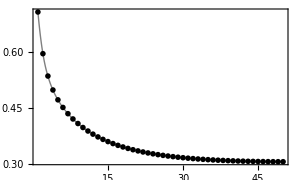
{-Graphics-,-Graphics-}

```mathematica
Module[{M,L,data,f,fdat,maxs,mins,ldat,fit},
M=TensorLoad["MA"];
L=Length[M];
data=MapIndexed[{First[#2],#1}&,Re@Mean[Join[Diagonal[M,#],Diagonal[M,L-#]]]&/@Range[L/2]];
f=Interpolation[data,InterpolationOrder->3];
fdat={#,f[#]}&/@Range[1,50,0.1];
maxs=ReplaceList[fdat,{___,{x1_,y1_},{x2_,y2_},{x3_,y3_},___}/;y2>y3&&y2>y1:>{x2,y2}];
mins=ReplaceList[fdat,{___,{x1_,y1_},{x2_,y2_},{x3_,y3_},___}/;y2<y3&&y2<y1:>{x2,y2}];
ldat={Log[#1],Log[#2]}&@@@maxs;
fit=Fit[ldat⟦1;;5⟧,{1,x},x];
{Graphics[{{Gray,Line[fdat]},{Dashed,{ColorData["HTML","Firebrick"],Line[maxs]},{ColorData["HTML","RoyalBlue"],Line[mins]}},{PointSize[Absolute[4]],Point[data]}},Frame->True,AspectRatio->0.6,ImageSize->300],
Graphics[{{Line[Table[{x,fit},{x,1,3.2,0.1}]]},{PointSize[Absolute[4]],Point[ldat]}},PlotLabel->fit,Frame->True,GridLines->{Range[-10,10,0.1],Range[-10,10,0.1]},ImageSize->300]}
]
```

#### IDMRG

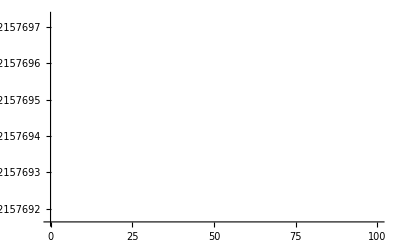

```mathematica
Module[{NA0,NB0,NA3,NB3,NAB0,vec,val,NAB3,data},
{NA0,NB0,NA3,NB3}=TensorLoad/@{"NA0","NB0","NA3","NB3"};
NAB0=NA0.NB0;
{val,vec}=First@Thread@Eigensystem@NAB0;
NAB3= NA3.NB0/val;
NAB0=NAB0/val;
data=Table[{l,Re[Conjugate[vec].NAB3.MatrixPower[NAB0,l].NAB3.vec]},{l,0,100}];
ListLinePlot[data]
]
```

## Code

#### I/O System

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### SYSVD

```mathematica
SYSVD[A_]:=Module[{U,S,V,Θ},
{U,S,V}=SingularValueDecomposition[A];
Θ=MatrixPower[Transpose[V].U,-1/2];
{U.Θ,S,V.Θ}];
```